Test graph:

```mathematica
Needs["PeterBurbery`MixedGraphs`"]
```

RandomWeightedMixedGraph::shdw: Symbol RandomWeightedMixedGraph appears in multiple contexts {PeterBurbery`MixedGraphs`,Global`}; definitions in context PeterBurbery`MixedGraphs` may shadow or be shadowed by other definitions.

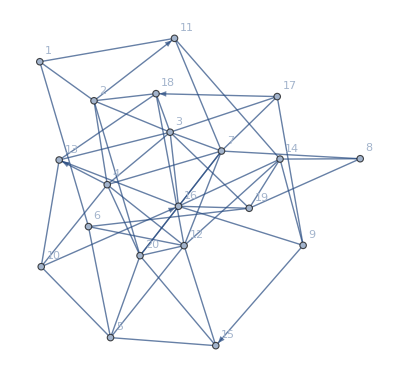

```mathematica
randomWeightedMixedGraph=RandomWeightedMixedGraph[{20,54},0.1,RandomReal[]&,VertexLabels->Automatic]
```

EulerianGraphQ::ngen: The generalized EulerianGraphQ[Graph[<20>, <54>]] is not implemented.

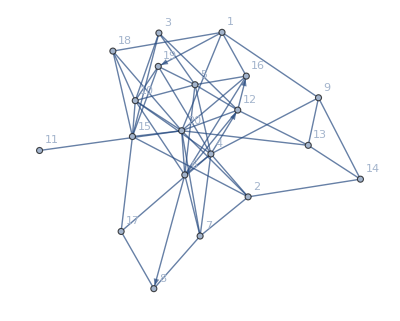
<|Acyclic→False,Bipartite→False,Complete→False,Connected→True,EdgeTransitive→False,WeightedEdge→True,Empty→False,Eulerian→EulerianGraphQ[-Graphics-],Hamiltonian→False,LoopFree→True,Mixed→True,Path→False,Planar→False,Simple→True,Tree→False,Undirected→False,VertexTransitive→False,WeightedVertex→False,WeaklyConnected→True,Weighted→True|>

```mathematica
GraphInformation[randomWeightedMixedGraph]
```

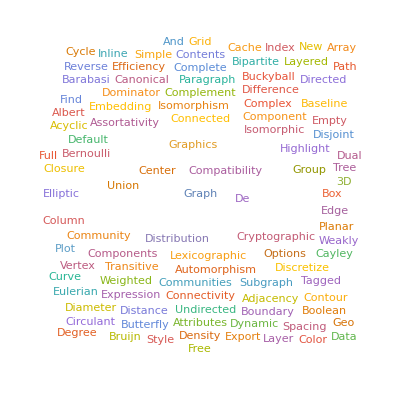

```mathematica
WordCloudFromNames[Names["*Graph*",IgnoreCase->True]]
```

```mathematica
AcyclicGraphQ[randomWeightedMixedGraph]
```

False

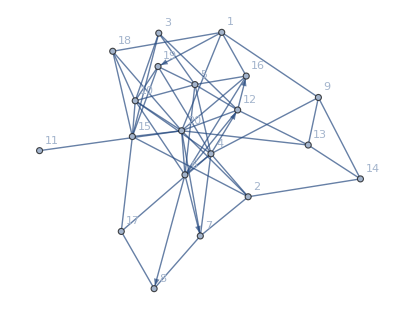

```mathematica
ConnectedGraphComponents[randomWeightedMixedGraph]
```

EulerianGraphQ::ngen: The generalized EulerianGraphQ[Graph[<20>, <54>]] is not implemented.

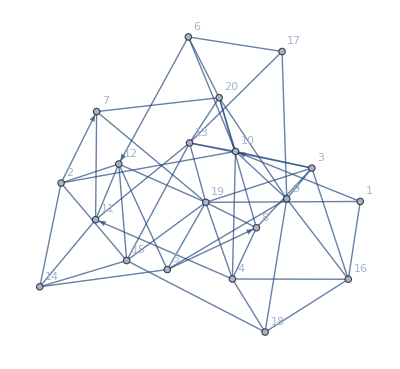
EulerianGraphQ[-Graphics-]

```mathematica
EulerianGraphQ[randomWeightedMixedGraph]
```

```mathematica
FindGraphCommunities[randomWeightedMixedGraph]
```

{{3,5,6,10,11,12,16,19,20},{1,9,13,14},{2,4,7,8},{15,17,18}}

```mathematica
FindGraphPartition[randomWeightedMixedGraph]
```

{{3,4,5,6,7,8,10,15,17,19},{1,2,9,11,12,13,14,16,18,20}}

```mathematica
FindGraphPartition[randomWeightedMixedGraph,3]
```

{{2,4,7,8,15,17,19},{3,5,6,10,12,16,20},{1,9,11,13,14,18}}

```mathematica
TimeConstrained[GraphCenter[randomWeightedMixedGraph],3]
```

```mathematica
randomWeightedMixedGraph
```

-Graphics-